```mathematica
μ=0.62;
γ=5/3;
```

```mathematica
years=365.25*86400;
tEnd=10^3 years;
```

```mathematica
rper=0.7Rsun;
θper=11*Pi/37;
kRoss=21.1;
χ=(16*T[Rper,zper]^3*sigmaSB*(γ-1)*μ*mP)/(3*kRoss*ρ[Rper,zper]^2*kB);  (*this is what Goldreich and Schubert call χ*)
ξradiative = (γ-1)*χ ;    (*this is what Balbus and Schaan call ξrad*)

ν=23;   (*from Menou&Balbus2004*)

η=596;     (*from Menou&Balbus2004*)


θper=11*Pi/36;

kR0=-1.227*10^-7;
kϕ0=4.552*10^-8;
kz0=-6.0152*10^-8;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=-99.67*Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vSqmod0=vR0^2+vz0^2;
SolveTheSystem;
δvϕsol[t_]=-(kR[t]*δvRsol[t]+kz[t]*δvzsol[t])/kϕ0;
vSqmod[t_]=δvRsol[t]^2+δvzsol[t]^2;
vSqmodTot[t_]=δvRsol[t]^2+δvϕsol[t]^2+δvzsol[t]^2;
MaxVelocitySq=(Max[vSqmod[tEnd/10^6],vSqmod[tEnd/10^5],vSqmod[tEnd/10^4],vSqmod[tEnd/10^3],vSqmod[tEnd/10^2],vSqmod[tEnd/10^1],vSqmod[tEnd]])/vSqmod0
MaxVelocitySqTot=(Max[vSqmodTot[tEnd/10^6],vSqmodTot[tEnd/10^5],vSqmodTot[tEnd/10^4],vSqmodTot[tEnd/10^3],vSqmodTot[tEnd/10^2],vSqmodTot[tEnd/10^1],vSqmodTot[tEnd]])/vSqmod0
```

0.416685

0.734634

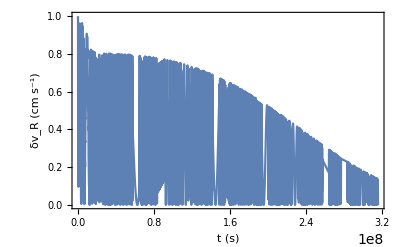

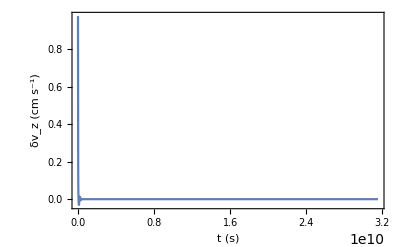

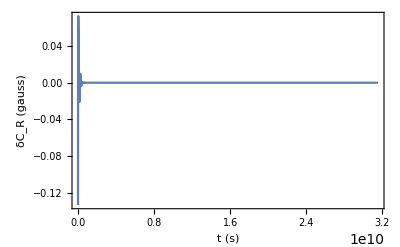

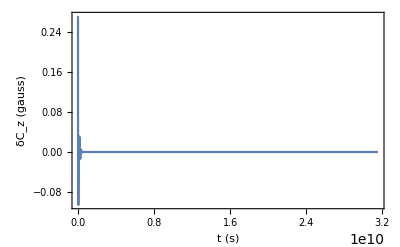

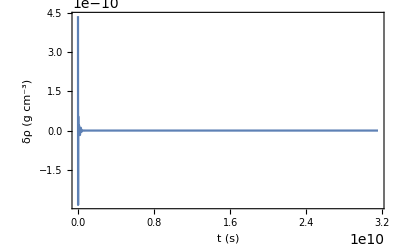

```mathematica
Plot[(δvRsol[t]^2+δvzsol[t]^2+δvϕsol[t]^2)/vSqmod0,{t,0,tEnd/100},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δv_R (cm s^-1)","Test 08 - δv_R(t)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δvzsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δv_z (cm s^-1)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δCRsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δC_R (gauss)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δCzsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δC_z (gauss)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δρsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δρ (g cm^-3)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
```